```mathematica
ClearAll["Global`*"]
```

### Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

#### Helper func

```mathematica
makeErrorData[x_,y_,yErr_]:=Module[{zeList,xy,errorB},
xy=Partition[Riffle[x,y],2];
errorB=Map[ErrorBar,yErr];
zeList=Partition[Riffle[xy,errorB],2]
];
```

```mathematica
Needs["ComputerArithmetic`"]
```

## Initialize orbit 1607 J-V, J_E-V data

### pot offset (in V)?

```mathematica
potTFactor=0;
```

### And the data ...

```mathematica
time={"01:03:50.199","01:03:50.830","01:03:51.461","01:03:52.092","01:03:52.723","01:03:53.354","01:03:53.985","01:03:54.616","01:03:55.248","01:03:55.879","01:03:56.510","01:03:57.141","01:03:57.772","01:03:58.403","01:03:59.034","01:03:59.665","01:04:00.296","01:04:00.927","01:04:01.558","01:04:02.189","01:04:02.820","01:04:03.451","01:04:04.083","01:04:04.714","01:04:05.345","01:04:05.976","01:04:06.607","01:04:07.238","01:04:07.869","01:04:08.500","01:04:09.131","01:04:09.762","01:04:10.393","01:04:11.024","01:04:11.656","01:04:12.287","01:04:12.918","01:04:13.549","01:04:14.180","01:04:14.811","01:04:15.442","01:04:16.073","01:04:16.704","01:04:17.335","01:04:17.966","01:04:18.597","01:04:19.229","01:04:19.860","01:04:20.491","01:04:21.122","01:04:21.753","01:04:22.384","01:04:23.015","01:04:23.646","01:04:24.277","01:04:24.908","01:04:25.539","01:04:26.171","01:04:26.802","01:04:27.433","01:04:28.064","01:04:28.695","01:04:29.326","01:04:29.957","01:04:30.588","01:04:31.219","01:04:31.850","01:04:32.481","01:04:33.113","01:04:33.744","01:04:34.375","01:04:35.006","01:04:35.637","01:04:36.268","01:04:36.899","01:04:37.530","01:04:38.161","01:04:38.792","01:04:39.424","01:04:40.055","01:04:40.686","01:04:41.317","01:04:41.948","01:04:42.579","01:04:43.210","01:04:43.841","01:04:44.472","01:04:45.103","01:04:45.735","01:04:46.366","01:04:46.997","01:04:47.628","01:04:48.259","01:04:48.890","01:04:49.521","01:04:50.152","01:04:50.783","01:04:51.414","01:04:52.046","01:04:52.677","01:04:53.308","01:04:53.939","01:04:54.570","01:04:55.201","01:04:55.832","01:04:56.463","01:04:57.094","01:04:57.725","01:04:58.357","01:04:58.988","01:04:59.619","01:05:00.250","01:05:00.881","01:05:01.512","01:05:02.143","01:05:02.774","01:05:03.405","01:05:04.037","01:05:04.668","01:05:05.299","01:05:05.930","01:05:06.561","01:05:07.192","01:05:07.823","01:05:08.454","01:05:09.085","01:05:09.717","01:05:10.348","01:05:10.979","01:05:11.610","01:05:12.241","01:05:12.872","01:05:13.503","01:05:14.134","01:05:14.766","01:05:15.397","01:05:16.028","01:05:16.659","01:05:17.290","01:05:17.921","01:05:18.552","01:05:19.183","01:05:19.814","01:05:20.446","01:05:21.077","01:05:21.708","01:05:22.339","01:05:22.970","01:05:23.601","01:05:24.232","01:05:24.863","01:05:25.495","01:05:26.126","01:05:26.757","01:05:27.388","01:05:28.019","01:05:28.650","01:05:29.281","01:05:29.912","01:05:30.544","01:05:31.175","01:05:31.806","01:05:32.437","01:05:33.068","01:05:33.699","01:05:34.330","01:05:34.961","01:05:35.593","01:05:36.224","01:05:36.855","01:05:37.486","01:05:38.117","01:05:38.748","01:05:39.379","01:05:40.010","01:05:40.642","01:05:41.273","01:05:41.904","01:05:42.535","01:05:43.166","01:05:43.797","01:05:44.428","01:05:45.059","01:05:45.691","01:05:46.322","01:05:46.953","01:05:47.584","01:05:48.215","01:05:48.846","01:05:49.477","01:05:50.109","01:05:50.740","01:05:51.371","01:05:52.002","01:05:52.633","01:05:53.264","01:05:53.895","01:05:54.527","01:05:55.158","01:05:55.789","01:05:56.420","01:05:57.051","01:05:57.682","01:05:58.313","01:05:58.944","01:05:59.576","01:06:00.207","01:06:00.838","01:06:01.469","01:06:02.100","01:06:02.731","01:06:03.362","01:06:03.994","01:06:04.625"}; pots={101.92,117.60,117.60,101.92,235.20,282.24,344.96,344.96,282.24,101.92,101.92,101.92,117.60,172.48,141.12,141.12,172.48,172.48,117.60,141.12,172.48,172.48,101.92,101.92,203.84,203.84,282.24,203.84,282.24,344.96,344.96,282.24,203.84,203.84,141.12,117.60,141.12,235.20,235.20,282.24,282.24,235.20,203.84,141.12,117.60,101.92,101.92,101.92,141.12,101.92,101.92,117.60,141.12,141.12,141.12,141.12,101.92,101.92,101.92,141.12,141.12,141.12,141.12,117.60,141.12,101.92,117.60,172.48,172.48,203.84,282.24,235.20,203.84,203.84,235.20,282.24,282.24,282.24,344.96,407.68,282.24,282.24,407.68,407.68,407.68,282.24,282.24,407.68,407.68,407.68,344.96,282.24,470.40,470.40,407.68,344.96,172.48,101.92,203.84,172.48,101.92,203.84,203.84,344.96,282.24,235.20,235.20,172.48,172.48,172.48,172.48,203.84,203.84,203.84,172.48,172.48,141.12,172.48,172.48,141.12,141.12,172.48,172.48,172.48,203.84,235.20,282.24,282.24,282.24,282.24,282.24,282.24,282.24,282.24,282.24,282.24,344.96,282.24,282.24,282.24,282.24,282.24,282.24,282.24,282.24,235.20,203.84,203.84,172.48,172.48,172.48,172.48,172.48,141.12,117.60,117.60,172.48,172.48,203.84,172.48,141.12,141.12,141.12,141.12,172.48,172.48,203.84,172.48,203.84,203.84,172.48,172.48,203.84,203.84,203.84,203.84,235.20,203.84,172.48,172.48,141.12,141.12,141.12,117.60,117.60,101.92,101.92,101.92,117.60,117.60,117.60,117.60,117.60,101.92,101.92,101.92,101.92,101.92,101.92,101.92,101.92,101.92,101.92,101.92,101.92,117.60,117.60,101.92,101.92,101.92,101.92,101.92,101.92,101.92}+potTFactor; curs={0.154,0.112,0.123,0.387,0.838,0.949,1.082,1.086,0.860,0.244,0.131,0.161,0.525,0.603,0.460,0.537,0.554,0.652,0.475,0.552,0.689,0.654,0.389,0.717,1.260,0.776,1.552,1.104,1.397,1.447,1.129,1.059,0.734,0.759,0.492,0.403,0.406,0.568,1.024,1.247,1.170,0.863,0.699,0.556,0.457,0.348,0.061,0.100,0.434,0.220,0.656,0.441,0.411,0.863,0.808,0.744,0.324,0.242,0.347,0.607,0.646,0.763,0.721,0.670,0.580,0.309,0.613,0.885,0.794,1.026,1.305,0.991,0.914,0.965,1.256,1.476,1.529,1.125,1.768,2.266,1.356,1.314,2.481,2.244,1.978,1.189,1.099,1.776,2.359,2.121,1.727,1.492,2.425,2.366,1.795,1.622,0.920,0.216,0.747,0.732,0.171,0.794,1.770,1.851,1.699,1.311,1.597,1.616,1.459,1.278,1.056,1.166,1.352,1.068,0.774,0.789,0.582,0.680,0.580,0.518,0.497,0.762,0.661,0.705,0.823,0.980,1.306,1.457,1.522,1.349,1.363,1.376,1.414,1.211,1.492,1.738,2.090,1.673,1.969,1.747,1.772,1.720,1.590,1.649,1.731,1.452,1.283,1.081,0.995,0.829,0.859,1.018,0.728,0.837,0.596,0.572,0.970,1.084,1.551,1.017,1.066,1.092,1.277,0.970,1.380,1.485,1.811,1.458,1.581,1.869,1.611,1.317,1.574,1.584,1.503,1.503,1.798,1.680,1.386,1.205,0.968,0.632,0.636,0.632,0.568,0.267,0.190,0.298,0.574,0.690,0.720,0.671,0.528,0.231,0.127,0.106,0.138,0.166,0.165,0.131,0.241,0.194,0.112,0.107,0.078,0.069,0.071,0.054,0.105,0.237,0.516,0.230,0.189,0.158};
curErrs={0.020,0.017,0.018,0.021,0.033,0.041,0.050,0.042,0.039,0.028,0.014,0.016,0.029,0.036,0.031,0.026,0.027,0.037,0.029,0.030,0.033,0.041,0.028,0.026,0.040,0.045,0.055,0.060,0.054,0.070,0.060,0.059,0.040,0.049,0.044,0.035,0.038,0.048,0.052,0.057,0.064,0.062,0.053,0.046,0.030,0.043,0.024,0.016,0.024,0.044,0.041,0.044,0.035,0.032,0.030,0.028,0.021,0.021,0.022,0.028,0.025,0.027,0.025,0.026,0.025,0.032,0.027,0.034,0.026,0.034,0.041,0.035,0.031,0.040,0.039,0.045,0.040,0.031,0.039,0.044,0.032,0.036,0.056,0.051,0.047,0.043,0.040,0.052,0.056,0.064,0.060,0.057,0.062,0.070,0.056,0.056,0.029,0.033,0.041,0.037,0.025,0.033,0.043,0.051,0.048,0.046,0.051,0.047,0.039,0.060,0.048,0.052,0.053,0.060,0.048,0.051,0.035,0.045,0.040,0.039,0.035,0.057,0.050,0.057,0.052,0.050,0.063,0.055,0.056,0.061,0.057,0.059,0.058,0.070,0.081,0.082,0.085,0.090,0.104,0.094,0.078,0.100,0.096,0.079,0.079,0.074,0.095,0.073,0.063,0.052,0.056,0.053,0.043,0.053,0.043,0.043,0.050,0.079,0.086,0.077,0.059,0.082,0.085,0.092,0.080,0.115,0.109,0.085,0.087,0.151,0.119,0.105,0.127,0.178,0.150,0.122,0.128,0.164,0.141,0.211,0.232,0.027,0.026,0.027,0.026,0.024,0.019,0.021,0.024,0.032,0.034,0.029,0.028,0.020,0.016,0.017,0.014,0.021,0.019,0.016,0.021,0.022,0.014,0.022,0.012,0.019,0.031,0.027,0.025,0.026,0.031,0.032,0.016,0.018};
jes={0.050,0.041,0.055,0.113,0.227,0.311,0.380,0.358,0.250,0.077,0.045,0.048,0.119,0.146,0.109,0.121,0.125,0.149,0.094,0.119,0.149,0.156,0.099,0.153,0.305,0.184,0.422,0.288,0.416,0.452,0.344,0.310,0.178,0.179,0.108,0.082,0.085,0.138,0.281,0.368,0.347,0.224,0.172,0.118,0.099,0.078,0.021,0.031,0.098,0.063,0.139,0.103,0.102,0.195,0.190,0.156,0.101,0.085,0.100,0.168,0.172,0.209,0.185,0.168,0.163,0.106,0.144,0.234,0.210,0.307,0.396,0.278,0.257,0.256,0.369,0.450,0.495,0.357,0.619,0.852,0.436,0.431,1.069,0.951,0.826,0.413,0.376,0.721,0.999,0.797,0.611,0.492,1.024,1.009,0.699,0.580,0.269,0.082,0.216,0.229,0.086,0.222,0.471,0.596,0.555,0.389,0.419,0.345,0.299,0.283,0.248,0.310,0.355,0.285,0.205,0.214,0.157,0.178,0.148,0.154,0.133,0.217,0.179,0.205,0.241,0.308,0.436,0.495,0.503,0.438,0.435,0.442,0.475,0.408,0.505,0.552,0.697,0.541,0.645,0.562,0.565,0.548,0.534,0.539,0.542,0.425,0.350,0.276,0.259,0.202,0.234,0.272,0.199,0.217,0.149,0.138,0.235,0.257,0.370,0.240,0.230,0.229,0.266,0.226,0.295,0.325,0.419,0.297,0.369,0.419,0.352,0.303,0.388,0.424,0.388,0.386,0.458,0.411,0.324,0.286,0.217,0.145,0.140,0.144,0.133,0.084,0.063,0.078,0.126,0.158,0.156,0.137,0.117,0.067,0.053,0.050,0.055,0.067,0.091,0.065,0.088,0.079,0.060,0.060,0.052,0.060,0.046,0.039,0.054,0.081,0.125,0.071,0.062,0.058};
jeErrs={0.100,0.030,0.051,0.042,0.077,0.108,0.059,0.053,0.055,0.060,0.024,0.030,0.177,0.078,0.050,0.042,0.049,0.123,0.074,0.055,0.044,0.081,0.060,0.060,0.066,0.082,0.058,0.054,0.062,0.099,0.077,0.069,0.042,0.045,0.049,0.044,0.090,0.081,0.066,0.069,0.075,0.073,0.060,0.061,1.371,0.199,0.244,34.469,0.081,0.035,0.060,0.043,0.045,0.055,0.163,0.042,0.118,0.035,0.039,0.054,0.066,0.055,0.046,0.043,0.048,0.043,0.038,0.052,0.092,0.064,0.099,0.050,0.111,0.050,0.063,0.067,0.068,0.102,0.063,0.063,0.054,0.079,0.106,0.083,0.081,0.063,0.070,0.084,0.096,0.091,0.084,0.083,0.100,0.103,0.081,0.084,0.060,0.033,0.066,0.063,0.027,0.056,0.058,0.078,0.076,0.076,0.074,0.052,0.048,0.068,0.049,0.079,0.059,0.069,0.070,0.085,0.066,0.072,0.044,0.080,0.038,0.083,0.055,0.074,0.067,0.065,0.103,0.091,0.089,0.100,0.078,0.080,0.084,0.106,0.112,0.102,0.118,0.115,0.138,0.117,0.122,0.126,0.117,0.109,0.099,0.083,0.102,0.077,0.074,0.054,0.072,0.098,0.114,0.066,0.058,0.053,0.078,0.078,0.162,0.071,0.064,0.156,0.122,0.114,0.146,0.153,0.113,0.090,0.114,0.127,0.108,0.105,0.177,3.788,0.590,0.274,0.424,0.213,0.247,0.251,4.130,0.043,0.039,0.504,0.071,0.028,0.053,0.053,0.327,0.049,0.053,0.032,0.053,0.063,0.031,0.027,0.060,0.066,0.096,0.045,0.087,0.073,0.039,0.059,0.021,0.027,0.032,0.059,0.034,0.031,0.046,0.027,0.029,0.190};
```

## Manip plots to decide on indices to use

### Check out J-V relation

```mathematica
ind1Start=0;ind1End=90;ind1Init=54;ind2Init=98;(*Good J-V relationship*)
```

```mathematica
ind1Start=0;ind1End=90;ind1Init=65;ind2Init=97;(*Good J-V relationship #2*)
```

```mathematica
ind1Start=0;ind1End=140;ind1Init=136;ind2Init=190;(*Super kappa J-V*)
```

```mathematica
ind1Start=0;ind1End=65;ind1Init=54;ind2Init=190;(*Super kappa J-V alt?*)
```

```mathematica
ind1Start=0;ind1End=140;ind1Init=136;ind2Init=158;(*Jim alt?*)
```

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],curs[[#1;;#2]],curErrs[[#1;;#2]]])&[ind1,ind2],AxesStyle->(FontSize->24),PlotRange->{{000,Max[pots]},{0,Max[curs]}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

### Check out energy flux–voltage relation

```mathematica
ind1Start=0;ind1End=80;ind1Init=54;ind2Init=98;(*Good J-V relationship*)
```

```mathematica
ind1Start=0;ind1End=166;ind1Init=166;ind2Init=190; (*Super kappa J-V*)
```

```mathematica
ind1Start=0;ind1End=166;ind1Init=90;ind2Init=173;
```

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],jes[[#1;;#2]],jeErrs[[#1;;#2]]])&[ind1,ind2],PlotRange->{{0,Max[pots]},{0,Max[jes]}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

The fits—J-V, J_E-V, and combined

## Initialize data for portions of arc in which we are interested

### Setup indices

```mathematica
inds1=Range[54,98];
```

```mathematica
inds1=Range[65,97]; (*Alternative good J-V*)
```

```mathematica
inds1=Range[112,199]; (*Marked J-V*)
```

```mathematica
inds2=Range[166,190]; (*Super-low kappa*)
```

```mathematica
(*inds2=Range[90,173]; (*Alt super-low kappa; perhaps too many points*)*)
```

```mathematica
inds2=Range[136,158]; (*Jim alt*)
```

```mathematica
inds3={3,4}~Join~inds2;
```

### Initialize plotData1, errorData1, plotDataWts1, etc.

Current data

```mathematica
{plotData1,plotData2,plotData3}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorData1,errorData2,errorData3}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{plotDataWts1,plotDataWts2,plotDataWts3}=(1/(curErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

Energy flux data

```mathematica
{jeData1,jeData2,jeData3}=(Partition[Riffle[pots[[#]],jes[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorJe1,errorJe2,errorJe3}=(makeErrorData[pots[[#]],jes[[#]],jeErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{jeDataWts1,jeDataWts2,jeDataWts3}=(1/(jeErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

## Fits: Select indices to use, setup bounds and initial guesses

### Which to use?

```mathematica
useinds1=0; (*Else use inds2*)
```

### Bounds

```mathematica
minFitT=20;
maxFitT=5000;
minFitRB=3;
maxFitRB=1000000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.501;
maxFitKappa=35;
```

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

### Initial guesses

```mathematica
kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;
```

```mathematica
gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;
```

#### Init fit data

Maxwellian-ish thing?

```mathematica
If[useinds1==1,Print["Using inds1 ..."];indsInUse=inds1;jData=plotData1;jWts=plotDataWts1;jErrData=errorData1;jeData=jeData1;jeWts=jeDataWts1;jeErrData=errorJe1;,Print["Using inds2 ..."];indsInUse=inds2;jData=plotData2;jWts=plotDataWts2;jErrData=errorData2;jeData=jeData2;jeWts=jeDataWts2;jeErrData=errorJe2;];
```

Using inds2 ...

## Nonlinear J-V fits

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,10<kFitT<4000,3<kFitRB<1000000,1.501<kFitKappa<20};
gConstraints={0.01<gFitN<10,10<gFitT<4000,3<gFitRB<1000000};*)
```

```mathematica
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[jData,{kModel,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jWts];
```

```mathematica
gFit=NonlinearModelFit[jData,{gModel,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB,gFitRBinit}},pot,Weights->jWts];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*jWts]/kDOF};
```

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*jWts]/gDOF};
```

## Nonlinear J_E-V fits

### Initial guesses

```mathematica
(*kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;*)
```

```mathematica
(*gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;*)
```

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,100<kFitT<4000,3<kFitRB<1000,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,100<gFitT<4000,3<gFitRB<1000};*)
```

```mathematica
kModelJeV = JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModelJeV = JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFitJeV=NonlinearModelFit[jeData,{kModelJeV,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jeWts];
```

```mathematica
gFitJeV=NonlinearModelFit[jeData,{gModelJeV,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitRBinit},{gFitRB,gFitRBinit}},pot,Weights->jeWts];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestJeVN,kBestJeVT,kBestJeVRB,kBestJeVKappa,kBestJeVChi2red}=Values@kFitJeV["BestFitParameters"]~Join~{Total[(kFitJeV["FitResiduals"])^2*jeWts]/kDOF};
```

```mathematica
{gBestJeVN,gBestJeVT,gBestJeVRB,gBestJeVChi2red}=Values@gFitJeV["BestFitParameters"]~Join~{Total[(gFitJeV["FitResiduals"])^2*jeWts]/gDOF};
```

## Now J-V and J_E-V fits simultaneously!

```mathematica
(*RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;*)
```

```mathematica
(*RBinit=kBestJeVRB;Tminit=kBestJeVT;nminit=kBestJeVN;kappainit=kBestJeVKappa;*)
```

```mathematica
combDat = Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=jWts~Join~jeWts;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]];
```

```mathematica
gCombFitModel[set_,pot_,gFitRB,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]];
```

```mathematica
kCombFit=NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB,kFitRBinit},{kFitT,kFitTinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->combWts];
```

```mathematica
gCombFit=NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB,gFitT,gFitN],gCombConstraints},{{gFitRB,gFitRBinit},{gFitT,gFitTinit},{gFitN,gFitNinit}},{set,pot},Weights->combWts];
```

```mathematica
kCombDOF=Length[combDat[[;;,1]]]-4;
```

```mathematica
gCombDOF=Length[combDat[[;;,1]]]-3;
```

```mathematica
{kCombRB,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF};
```

```mathematica
{gCombRB,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF};
```

Plots

### Setup plot ranges

```mathematica
minPot=Min[pots[[;;]] ]* 8/10;maxPot=400;
```

```mathematica
minJ=0;maxJ=2.5;
```

```mathematica
minJe=0;maxJe=1.;
```

### Setup combined fit plots

```mathematica
parNames={"T_m : ","n_m : ","R_B : ","χ_red^2:"};
vSpace=0.5;
pTableFontSize=16;
```

```mathematica
JVRepl={gRB->gBestRB,gTm->gBestT,gnm->gBestN,gChi2->gBestChi2red,kRB->kBestRB,kTm->kBestT,knm->kBestN,kappa->kBestKappa,kChi2->kBestChi2red};
```

```mathematica
JeVRepl={gRB->gBestJeVRB,gTm->gBestJeVT,gnm->gBestJeVN,gChi2->gBestJeVChi2red,kRB->kBestJeVRB,kTm->kBestJeVT,knm->kBestJeVN,kappa->kBestJeVKappa,kChi2->kBestJeVChi2red};
```

```mathematica
combRepl={gRB->gCombRB,gTm->gCombT,gnm->gCombN,gChi2->gCombChi2red,kRB->kCombRB,kTm->kCombT,knm->kCombN,kappa->kCombKappa,kChi2->kCombChi2red};
```

```mathematica
(*gVals=MapThread[NumberForm,{({gTm,gnm,gRB}/.combRepl),{{3,0},{3,2},{3,1}}}];
kVals=MapThread[NumberForm,{({kTm,knm,kRB}/.combRepl),{{3,0},{3,2},{3,1}}}];*)
```

```mathematica
gJVVals=(MapThread[NumberForm,{({gTm,gnm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JVRepl}~Join~{NumberForm[gChi2,3]/.JVRepl};
kJVVals=(MapThread[NumberForm,{({kTm,knm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JVRepl}~Join~{NumberForm[kChi2,3]/.JVRepl};
```

```mathematica
gJeVVals=(MapThread[NumberForm,{({gTm,gnm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JeVRepl}~Join~{NumberForm[gChi2,3]/.JeVRepl};
kJeVVals=(MapThread[NumberForm,{({kTm,knm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JeVRepl}~Join~{NumberForm[kChi2,4]/.JeVRepl};
```

```mathematica
gCombVals=(MapThread[NumberForm,{({gTm,gnm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.combRepl}~Join~{NumberForm[gChi2,4]/.combRepl};
kCombVals=(MapThread[NumberForm,{({kTm,knm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.combRepl}~Join~{NumberForm[kChi2,4]/.combRepl};
```

```mathematica
JVParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gJVVals~Join~{""}~Join~kJVVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
JeVParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gJeVVals~Join~{""}~Join~kJeVVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gCombVals~Join~{""}~Join~kCombVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combTitle=StringJoin@Riffle[time[[indsInUse[[{1,-1}]]]],"–"];
```

```mathematica
combFitJVPlot=Plot[Evaluate@(({JVMaxwellian[pot,gRB,gTm,gnm],JVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,600},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.combRepl),{3,3}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",combTitle],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[combParTable,Scaled[{0.12,0.7}]]];
```

```mathematica
combFitJeVPlot=Plot[Evaluate@(({JEVMaxwellian[pot,gRB,gTm,gnm],JEVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,600},PlotRange->{{minPot,maxPot},{0,1.5}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,23]];
```

```mathematica
combJVPlot=Show[combFitJVPlot,ErrorListPlot[jErrData,PlotStyle->Gray]];
```

```mathematica
combJeVPlot=Show[combFitJeVPlot,ErrorListPlot[jeErrData,PlotStyle->Gray]];
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
```

```mathematica
If[!FileExistsQ[dir],Print["Nei!"];CreateDirectory[dir];Print["Nå har du det!"],Print["Ja!"]]
```

Ja!

```mathematica
orbPref="Orb1607";
```

```mathematica
JVPref="JVFit";
JeVPref="JeVFit";
combPref="combJVJeVFit";
```

```mathematica
(*combJVPref="combJVJeVFit__JV";
combJeVPref="combJVJeVFit__JeV";*)
```

```mathematica
(*{JVFilename,JeVFilename,combJVFilename,combJeVFilename}=(ToString@StringForm["`1`__`2`__inds_`3`-`4`.png",orbPref,#,indsInUse[[1]],indsInUse[[-1]]])&/@{JVPref,JeVPref,combJVPref,combJeVPref}*)
```

```mathematica
If[potTFactor == 0,suffString="",suffString=ToString@StringForm["__`1`V_offset",potTFactor]];
```

```mathematica
{JVFilename,JeVFilename,combFilename}=(ToString@StringForm["`1`__`2``3`__inds_`4`-`5`.png",orbPref,#,suffString,indsInUse[[1]],indsInUse[[-1]]])&/@{JVPref,JeVPref,combPref}
```

{Orb1607__JVFit__inds_136-158.png,Orb1607__JeVFit__inds_136-158.png,Orb1607__combJVJeVFit__inds_136-158.png}

### J-V plot

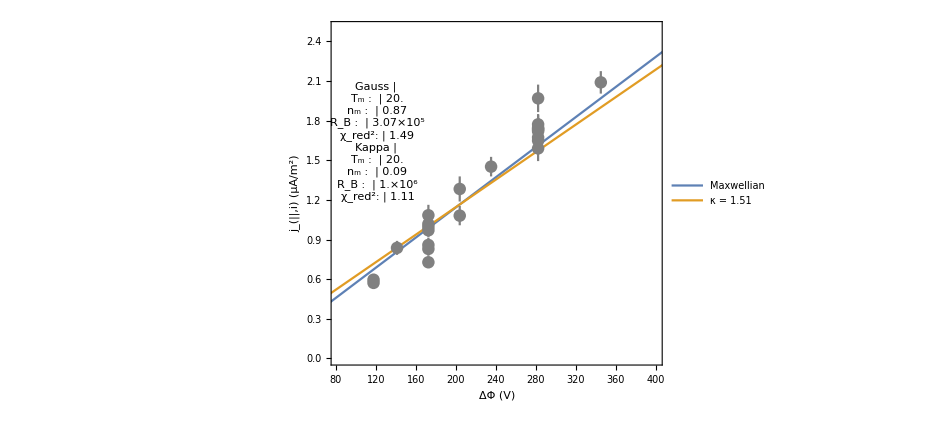

```mathematica
JVPlot=Show[Plot[{kFit[pot],gFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]
```

### J_E-V plot

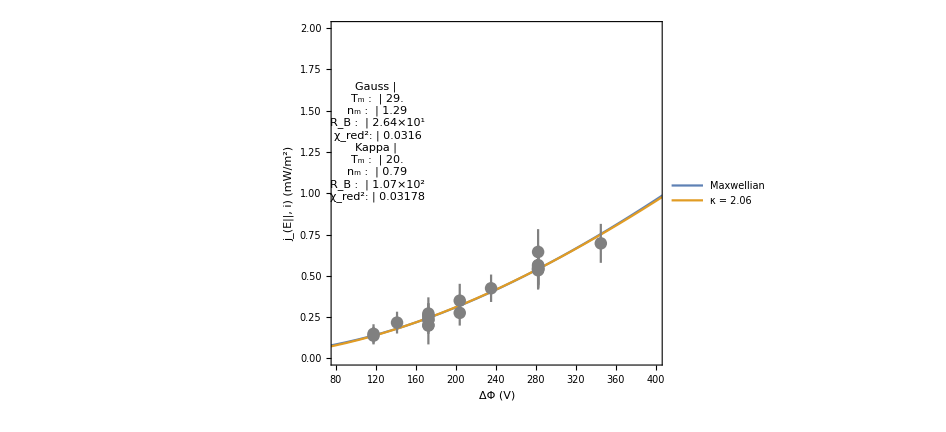

```mathematica
JeVPlot=Show[Plot[{kFitJeV[pot],gFitJeV[pot]},{pot,20,600},PlotRange->{{minPot,maxPot},{0.,2}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestJeVKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",Style[StringForm["J_E-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23],Epilog->Inset[JeVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jeErrData,PlotStyle->Gray]]
```

### Plots from combined fit

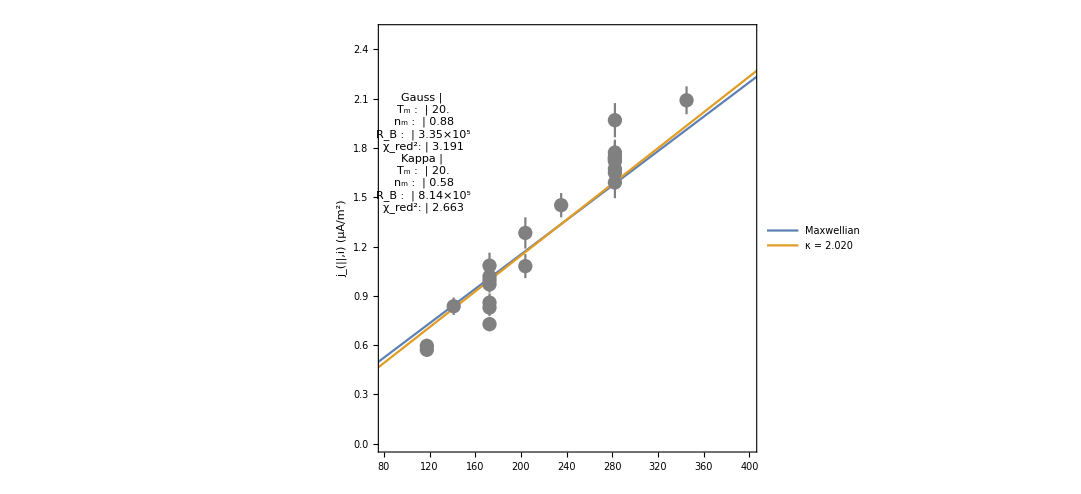
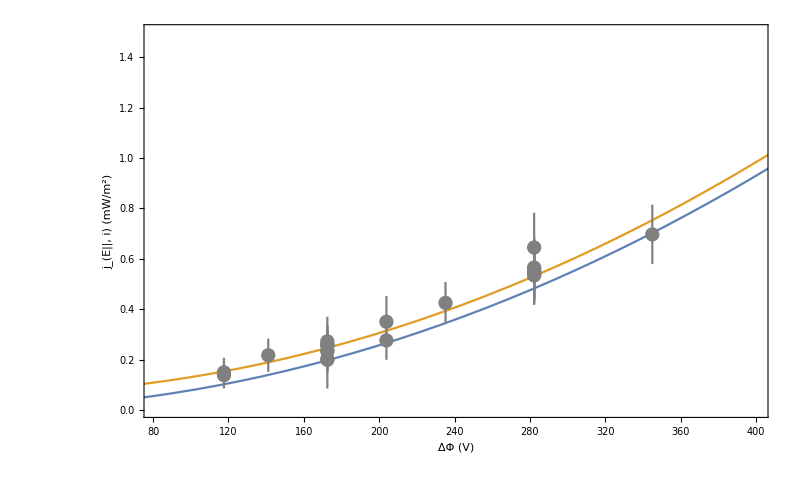

```mathematica
combPlot=Column[{combJVPlot,combJeVPlot}]
```

```mathematica
makePlots=1;
```

```mathematica
(*If[makePlots==1,Print["Making plots in "<>dir<>" ..."];Export[dir<>JVFilename,JVPlot];Export[dir<>JeVFilename,JeVPlot];Export[dir<>combJVFilename,combJVPlot];Export[dir<>combJeVFilename,combJeVPlot];Print["Done!"]]*)
```

```mathematica
If[makePlots==1,Print["Making plots in "<>dir<>" ..."];Export[dir<>JVFilename,JVPlot];Print[JeVFilename<>" ..."];Export[dir<>JeVFilename,JeVPlot];Print[combFilename<>" ..."];Export[dir<>combFilename,combPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/20180316/ ...

Orb1607__JeVFit__inds_136-158.png ...

Orb1607__combJVJeVFit__inds_136-158.png ...

Done!

Param tables

### J-V params

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.0788489 | 18.0635 | 0.0043651 | 0.996563
kFitT | 20.0084 | 211292. | 0.0000946954 | 0.999925
kFitRB | 999996. | 413.953 | 2415.72 | 1.33998×10^-53
kFitKappa | 1.5077 | 82.2571 | 0.0183292 | 0.985567

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.737783 | 2.50754 | 0.294226 | 0.771617
gFitT | 20. | 189.449 | 0.10557 | 0.916976
gFitRB | 336621. | 1.19817×10^10 | 0.0000280946 | 0.999978

### J_E-V params

```mathematica
kFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.590468 | 12.8417 | 0.0459806 | 0.963806
kFitT | 20.0001 | 209.717 | 0.0953669 | 0.925022
kFitRB | 239189. | 4.5854×10^9 | 0.0000521631 | 0.999959
kFitKappa | 2.43713 | 84.7723 | 0.0287491 | 0.977365

```mathematica
gFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.762078 | 0.387809 | 1.96508 | 0.063448
gFitT | 20. | 47.5033 | 0.421023 | 0.678228
gFitRB | 330538. | 6.09865×10^9 | 0.0000541986 | 0.999957

### Params from combined fit

```mathematica
kCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitRB | 805633. | 8.95543×10^9 | 0.0000899603 | 0.999929
kFitT | 20. | 157.058 | 0.127342 | 0.899278
kFitN | 0.491447 | 1.8178 | 0.270352 | 0.788213
kFitKappa | 2.0396 | 0.791263 | 2.57765 | 0.0135471

```mathematica
gCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitRB | 450860. | 4.64319×10^9 | 0.0000971014 | 0.999923
gFitT | 20. | 30.7434 | 0.650545 | 0.518801
gFitN | 0.738934 | 0.408339 | 1.80961 | 0.0773503

Mess ‘round, fit by eye

```mathematica
RBinit=gCombRB;Tminit=gCombT;nminit=gCombN;kappainit=kCombKappa;
```

```mathematica
Manipulate[Row[{Manipulate[Show[Plot[{JVMaxwellian[pot,RB,Tm,nm],JVKappa[pot,RB,Tm,nm,kappa]},{pot,100,1000},PlotRange->{{100,600},{0.,3}},PlotLegends->{"Maxwellian",StringForm["κ = `1`",NumberForm[kappa,{3,1}]]},FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->500,FrameStyle->(FontSize->18)],ErrorListPlot[jErrData]],{{RB,RBinit},1.01,100000},{{kappa,kappainit},1.501,35}],Manipulate[Show[Plot[{JEVMaxwellian[pot,RB,Tm,nm],JEVKappa[pot,RB,Tm,nm,kappa]},{pot,100,600},PlotRange->{Full,{0.,1.5}},PlotLegends->{"Maxwellian",StringForm["κ = `1`",NumberForm[kappa,{3,1}]]},FrameLabel->{"ΔΦ (V)","j_(E par, i) (mW/m^2)"},ImageSize->500,FrameStyle->(FontSize->18)],ErrorListPlot[jeErrData]],{{RB,RBinit},1.01,100000},{{kappa,kappainit},1.501,35}]}],{{Tm,Tminit},3,500},{{nm,nminit},0.1,5}]
```

Linear model, if we ever cared

## Linear model??

```mathematica
lm=LinearModelFit[plotData2,x,x,Weights->plotDataWts2]
```

FittedModel[0.571783+0.000828171 x]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.571783 | 0.209522 | 2.72899 | 0.0155285
x | 0.000828171 | 0.000104376 | 7.93453 | 9.52667×10^-7

```mathematica
Kmeas=(lm["BestFitParameters"])[[2]]
```

0.000828171

```mathematica
lm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
lm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | 0.571783 | 0.209522 | {0.125197,1.01837}
x | 0.000828171 | 0.000104376 | {0.000605699,0.00105064}

```mathematica
lm["AdjustedRSquared"]
```

0.794758

#### See it

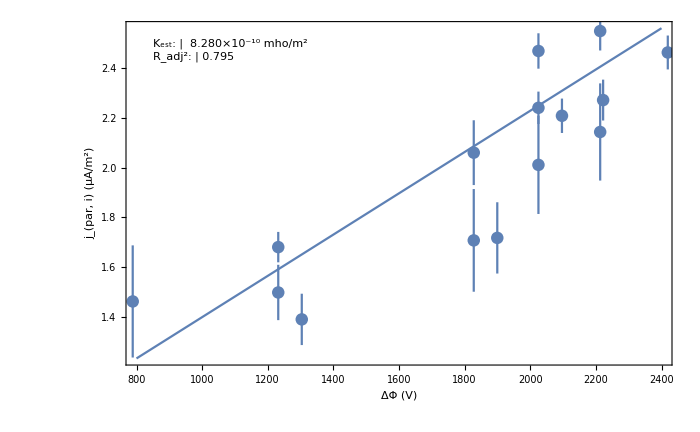

```mathematica
Show[Plot[lm[x],{x,800,2400},Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18),Epilog->Inset[TextGrid[Map[(Style[#,18])&,{{StringForm["K_est:"],StringForm[" `1` mho/m^2",NumberForm[Kmeas*1*^-6,{3,3},ScientificNotationThreshold->{-2,2}]]},{StringForm["R_adj^2:"],NumberForm[lm["AdjustedRSquared"],{3,3}]}},{2}]],Scaled[{0.05,0.95}],{-1,1}]],ErrorListPlot[errorData2]]
```

### Assess it

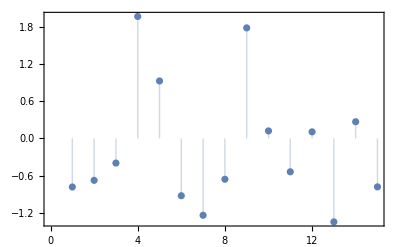

```mathematica
ListPlot[lm["StandardizedResiduals"],Frame->True,Filling->Axis]
```

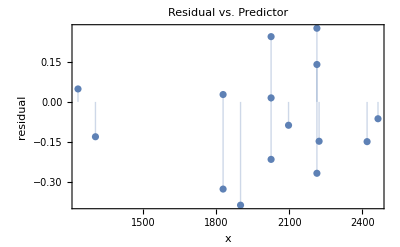

```mathematica
ListPlot[Transpose[{pots[[inds2]],lm["FitResiduals"]}],Frame->True,Filling->0,FrameLabel->{"x","residual"},PlotLabel->"Residual vs. Predictor"]
```

## Linear model for second half of arc

```mathematica
lm=LinearModelFit[plotData2,x,x,Weights->plotDataWts2]
```

FittedModel[0.571783+0.000828171 x]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.571783 | 0.209522 | 2.72899 | 0.0155285
x | 0.000828171 | 0.000104376 | 7.93453 | 9.52667×10^-7

```mathematica
Kmeas=(lm["BestFitParameters"])[[2]]
```

0.000828171

```mathematica
lm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
lm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | 0.571783 | 0.209522 | {0.125197,1.01837}
x | 0.000828171 | 0.000104376 | {0.000605699,0.00105064}

```mathematica
lm["AdjustedRSquared"]
```

0.794758

#### See it

```mathematica
Show[Plot[lm[x],{x,800,2400},Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18),Epilog->Inset[TextGrid[Map[(Style[#,18])&,{{StringForm["K_est:"],StringForm[" `1` mho/m^2",NumberForm[Kmeas*1*^-6,{3,3},ScientificNotationThreshold->{-2,2}]]},{StringForm["R_adj^2:"],NumberForm[lm["AdjustedRSquared"],{3,3}]}},{2}]],Scaled[{0.05,0.95}],{-1,1}]],ErrorListPlot[errorData2]]
```

-Graphics-

### Assess it

```mathematica
ListPlot[lm["StandardizedResiduals"],Frame->True,Filling->Axis]
```

-Graphics-

```mathematica
ListPlot[Transpose[{pots[[inds2]],lm["FitResiduals"]}],Frame->True,Filling->0,FrameLabel->{"x","residual"},PlotLabel->"Residual vs. Predictor"]
```

-Graphics-